```mathematica
d1n[n_,k_,s_]:=d1n[n,k,s]=Sum[ j^-s d1n[Floor[n/j],k-1,s],{j,1,n}];d1n[n_,0,s_]:=1
d2n[n_,k_,s_]:=d2n[n,k,s]=Sum[ j^-s d2n[Floor[n/j],k-1,s],{j,2,n}];d2n[n_,0,s_]:=1
lin[n_,s_]:=Sum[ (-1)^(k+1)/k d2n[n,k,s],{k,1,Log[2,n]}]
```

```mathematica
N[d2n[100,1,2]]
```

0.634984

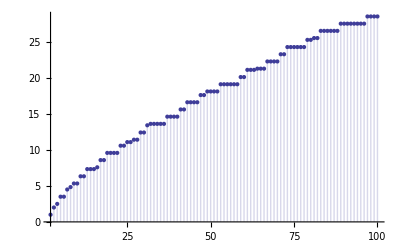

```mathematica
DiscretePlot[lin[n,0],{n,2,100}]
```

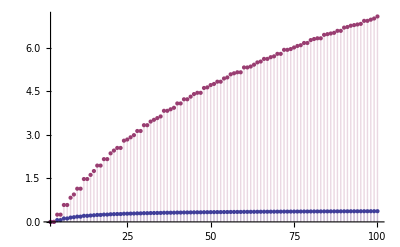

```mathematica
DiscretePlot[{d2n[n,2,2],d2n[n,2,1]},{n,2,100}]
```

```mathematica
Table[{n,d2n[n,1,-1],d2n[n,1,0],d2n[n,1,1]},{n,2,100}]//TableForm
```

2 | 2 | 1 | 1/2
3 | 5 | 2 | 5/6
4 | 9 | 3 | 13/12
5 | 14 | 4 | 77/60
6 | 20 | 5 | 29/20
7 | 27 | 6 | 223/140
8 | 35 | 7 | 481/280
9 | 44 | 8 | 4609/2520
10 | 54 | 9 | 4861/2520
11 | 65 | 10 | 55991/27720
12 | 77 | 11 | 58301/27720
13 | 90 | 12 | 785633/360360
14 | 104 | 13 | 811373/360360
15 | 119 | 14 | 835397/360360
16 | 135 | 15 | 1715839/720720
17 | 152 | 16 | 29889983/12252240
18 | 170 | 17 | 10190221/4084080
19 | 189 | 18 | 197698279/77597520
20 | 209 | 19 | 40315631/15519504
21 | 230 | 20 | 13684885/5173168
22 | 252 | 21 | 13920029/5173168
23 | 275 | 22 | 325333835/118982864
24 | 299 | 23 | 990874363/356948592
25 | 324 | 24 | 25128807667/8923714800
26 | 350 | 25 | 25472027467/8923714800
27 | 377 | 26 | 232222818803/80313433200
28 | 405 | 27 | 235091155703/80313433200
29 | 434 | 28 | 6897956948587/2329089562800
30 | 464 | 29 | 6975593267347/2329089562800
31 | 495 | 30 | 218572480850557/72201776446800
32 | 527 | 31 | 441657572729039/144403552893600
33 | 560 | 32 | 40548494360749/13127595717600
34 | 594 | 33 | 40934600117149/13127595717600
35 | 629 | 34 | 41309674280509/13127595717600
36 | 665 | 35 | 41674329717109/13127595717600
37 | 702 | 36 | 1555077795250633/485721041551200
38 | 740 | 37 | 1567859927923033/485721041551200
39 | 779 | 38 | 1580314313603833/485721041551200
40 | 819 | 39 | 1592457339642613/485721041551200
41 | 860 | 40 | 65776471966898333/19914562703599200
42 | 902 | 41 | 9464375460249419/2844937529085600
43 | 945 | 42 | 409813082319810617/122332313750680800
44 | 989 | 43 | 4538526983955586987/1345655451257488800
45 | 1034 | 44 | 4568430438427975627/1345655451257488800
46 | 1080 | 45 | 4597683817803138427/1345655451257488800
47 | 1127 | 46 | 217436794888004994869/63245806209101973600
48 | 1175 | 47 | 218754415850694619319/63245806209101973600
49 | 1224 | 48 | 10782212182893138320231/3099044504245996706400
50 | 1274 | 49 | 10844193072978058254359/3099044504245996706400
51 | 1325 | 50 | 10904958651492685640759/3099044504245996706400
52 | 1377 | 51 | 10964555661189724038959/3099044504245996706400
53 | 1430 | 52 | 584220494547301370771227/164249358725037825439200
54 | 1484 | 53 | 195754049779501924982009/54749786241679275146400
55 | 1539 | 54 | 196749500438441548166489/54749786241679275146400
56 | 1595 | 55 | 197727175192757249508389/54749786241679275146400
57 | 1652 | 56 | 198687697758400745563589/54749786241679275146400
58 | 1710 | 57 | 199631659590153836514389/54749786241679275146400
59 | 1769 | 58 | 11833017702060755629495351/3230237388259077233637600
60 | 1829 | 59 | 11886854991865073583389311/3230237388259077233637600
61 | 1890 | 60 | 728328391892028565820385571/197044480683803711251893600
62 | 1952 | 61 | 731506528677251206324448371/197044480683803711251893600
63 | 2015 | 62 | 244878072948945130739111857/65681493561267903750631200
64 | 2079 | 63 | 491808692571679883470430939/131362987122535807501262400
65 | 2144 | 64 | 493829661604334280508911899/131362987122535807501262400
66 | 2210 | 65 | 165273336631356557177219433/43787662374178602500420800
67 | 2277 | 66 | 11117101216675067933374122811/2933773379069966367528193600
68 | 2345 | 67 | 11160244942837861556426008011/2933773379069966367528193600
69 | 2414 | 68 | 33608290192820974511344467233/8801320137209899102584580800
70 | 2484 | 69 | 33734023337638258784238532673/8801320137209899102584580800
71 | 2555 | 70 | 2403916977109526272783520400583/624893729741902836283505236800
72 | 2627 | 71 | 7237788170067824769862373919949/1874681189225708508850515710400
73 | 2700 | 72 | 530233217604176916708803811866677/136851726813476721146087646859200
74 | 2774 | 73 | 532082565263818494021588780067477/136851726813476721146087646859200
75 | 2849 | 74 | 533907254954664850303536615358933/136851726813476721146087646859200
76 | 2925 | 75 | 535707935570631649265985137028133/136851726813476721146087646859200
77 | 3002 | 76 | 48862293702186674987753179690703/12441066073952429195098876987200
78 | 3080 | 77 | 49021794549288629208203165293103/12441066073952429195098876987200
79 | 3159 | 78 | 3885162835467754136643148935142337/982844219842241906412811281988800
80 | 3239 | 79 | 3897448388215782160473309076167197/982844219842241906412811281988800
81 | 3320 | 80 | 35186240407257844100527871827947973/8845597978580177157715301537899200
82 | 3402 | 81 | 35294113553338090163426838919873573/8845597978580177157715301537899200
83 | 3485 | 82 | 2938257022905641660722142931887405759/734184632222154704090370027645633600
84 | 3569 | 83 | 2946997316146381597675599717930806159/734184632222154704090370027645633600
85 | 3654 | 84 | 2955634782407818711841368777079578319/734184632222154704090370027645633600
86 | 3740 | 85 | 2964171813015053068865675405308015919/734184632222154704090370027645633600
87 | 3827 | 86 | 2972610716833698525234530233211988719/734184632222154704090370027645633600
88 | 3915 | 87 | 32790490964198453115591128818787580109/8076030954443701744994070304101969600
89 | 4004 | 88 | 2926429726768106029032604535176196599301/718766754945489455304472257065075294400
90 | 4094 | 89 | 2934416024045278134091543115810252991461/718766754945489455304472257065075294400
91 | 4185 | 90 | 2942314559813909886347636217536242829861/718766754945489455304472257065075294400
92 | 4277 | 91 | 2950127241932882597818337002939124083061/718766754945489455304472257065075294400
93 | 4370 | 92 | 2957855916717242699488277564843049623861/718766754945489455304472257065075294400
94 | 4464 | 93 | 2965502371557088331991516631407571701461/718766754945489455304472257065075294400
95 | 4559 | 94 | 2973068337398619799942090023587204072981/718766754945489455304472257065075294400
96 | 4655 | 95 | 2980555491095968648434844942931631940631/718766754945489455304472257065075294400
97 | 4752 | 96 | 289832649391254448353484431721433373535607/69720375229712477164533808935312303556800
98 | 4850 | 97 | 290544081791557636895979674669752886837207/69720375229712477164533808935312303556800
99 | 4949 | 98 | 291248328005999177069358804052937859600407/69720375229712477164533808935312303556800
100 | 5049 | 99 | 11677821270331852073640165685691639305439/2788815009188499086581352357412492142272